Authors:  Jozef Hanč, Martina Hančová 
Faculty of Science, P. J. Šafárik University in Košice, Slovakia
email: martina.hancova@upjs.sk

## Advanced Numerical Integration for f(x)

NIntegrate Integration Strategies
https://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html 
basic ideas + properties and comparison of methods

#### Numerical inversion of GDD characteristic function -Graphics-

```mathematica
phi[t_]:=a1*ArcTan[t/b1]-a2*ArcTan[t/b2]; phi[t]
```

a1 ArcTan[t/b1]-a2 ArcTan[t/b2]

```mathematica
r[t_]:=1/Pi*b1^a1*b2^a2/(b1^2+t^2)^(a1/2)/(b2^2+t^2)^(a2/2); r[t]
```

(b1^a1 b2^a2 (b1^2+t^2)^(-a1/2) (b2^2+t^2)^(-a2/2))/π

```mathematica
gc[x_,t_]:=r[t]*Cos[phi[t]]*Cos[x*t];
gs[x_,t_]:= r[t]*Sin[phi[t]]*Sin[x*t];
```

```mathematica
FullSimplify[ {gc[x,t], gs[x,t]}]
```

{(b1^a1 b2^a2 (b1^2+t^2)^(-a1/2) (b2^2+t^2)^(-a2/2) Cos[t x] Cos[a1 ArcTan[t/b1]-a2 ArcTan[t/b2]])/π,(b1^a1 b2^a2 (b1^2+t^2)^(-a1/2) (b2^2+t^2)^(-a2/2) Sin[t x] Sin[a1 ArcTan[t/b1]-a2 ArcTan[t/b2]])/π}

### Parameters

```mathematica
{a1,a2,b1, b2} ={1/2,17/2,1,93}
```

{1/2,17/2,1,93}

```mathematica
Prec=15
```

15

## Double-Exponential Quadrature for f(x) - default precision

Double Exponential Oscillatory Integration https://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html#48895312

```mathematica
Ifx[x_]:= 
NIntegrate[gc[x,t], {t, 0,Infinity},
Method->{"DoubleExponentialOscillatory","SymbolicProcessing"->0}] +
NIntegrate[gs[x,t], {t, 0,Infinity}, 
Method->{"DoubleExponentialOscillatory","SymbolicProcessing"->0}]
```

```mathematica
Res2=Ifx[-3]
```

4.96372×10^-9

### Test and Plots

```mathematica
Ifx[0.25] //TraditionalForm
```

0.689707

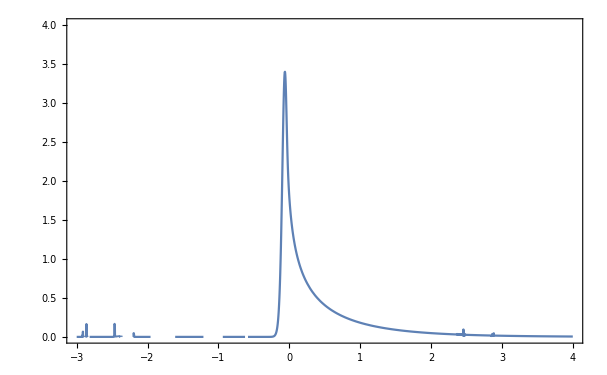

```mathematica
Plot[Ifx[z], {z,-3,4}, PlotRange ->{0,4}, Frame->True]
```

## Results - CSV file

```mathematica
$VersionNumber
```

12.3

```mathematica
$OutputSizeLimit=100
```

100

```mathematica
n = 10000-1;
```

```mathematica
dataset =Flatten[RepeatedTiming[Table[Ifx[x], {x,-3,4, 7/n}]]]
```

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (5595818096650401 √93 Sin[(9740 t)/3333] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞}. DoubleExponentialOscillatory obtained -0.00798575 and 1.28646×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {48.7522}. NIntegrate obtained 0.00160215 and 0.0337219 for the integral and error estimates.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (5595818096650401 √93 Sin[(29213 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞}. DoubleExponentialOscillatory obtained -0.00799227 and 1.8873×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {48.7522}. NIntegrate obtained 0.00330729 and 0.0352172 for the integral and error estimates.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (5595818096650401 √93 Sin[(29206 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞}. DoubleExponentialOscillatory obtained -0.0079988 and 2.3012×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::deoncon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {48.7522}. NIntegrate obtained 0.00498612 and 0.0410306 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-4073.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.26786×10^-103 2.36324×10^-206 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.98903×10^-103 1.35675×10^-206 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::deorela: The relative error 1.50082 is larger than expected for the integrand (5595818096650401 √93 Sin[(141 t)/1111] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

NIntegrate::deorela: The relative error 2.46463 is larger than expected for the integrand (5595818096650401 √93 Sin[(1262 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

NIntegrate::deorela: The relative error 4.33326 is larger than expected for the integrand (5595818096650401 √93 Sin[(1255 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

General::stop: Further output of NIntegrate::deorela will be suppressed during this calculation.

NIntegrate::deorel: The relative error 2.07172 is larger than expected for the integrand (5595818096650401 √93 Sin[(1241 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deorel: The relative error 8.28685 is larger than expected for the integrand (5595818096650401 √93 Sin[(1234 t)/9999] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

NIntegrate::deorel: The relative error 859.284 is larger than expected for the integrand (5595818096650401 √93 Sin[(409 t)/3333] Sin[17/2 ArcTan[t/93]-ArcTan[t]/2])/(π (1+t^2)^(1/4) (8649+t^2)^(17/4)) over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {10,5}.

General::stop: Further output of NIntegrate::deorel will be suppressed during this calculation.

{77.3717,4.96372×10^-9,4.96189×10^-9,4.96001×10^-9,4.95808×10^-9,4.9561×10^-9,4.95408×10^-9,4.95201×10^-9,4.94989×10^-9,4.94771×10^-9,4.9455×10^-9,9979,0.00470222,0.00469853,0.00469484,0.00469115,0.00468746,0.00468378,0.0046801,0.00467643,0.00467275,0.00466908,0.00466542}
 |  |  |  |

```mathematica
FileName = StringJoin["WolframNumInvDE",ToString[n+1],".txt"];
```

```mathematica
Export[FileName, dataset, "CSV"]
```

WolframNumInvDE10000.txt

```mathematica
SystemOpen[FileName]
```

## Export on the cloud

```mathematica
CopyFile[FileName,CloudObject[FileName],OverwriteTarget->True]
```

CloudObject[https://www.wolframcloud.com/obj/hancjozef/WolframNumInvDE10000.txt]
 |  |  |  |